```mathematica
Helver Jussef López Abril
Michael Velasquez Rico
```

Series de taylor

```mathematica
f[x_]:=√x
f''[x]
```

-1/(4 x^(3/2))

```mathematica
Series[f[x],{x,4,2}]//FullSimplify
```

2+(x-4)/4-1/64 (x-4)^2+O[x-4]^3

```mathematica
Normal[%]
```

2+1/4 (-4+x)-1/64 (-4+x)^2

```mathematica
Plot[{f[x],2+1/4 (-4+x)-1/64 (-4+x)^2},{x,0,2},PlotLegends->Automatic,PlotStyle->{Blue,Red}]
```

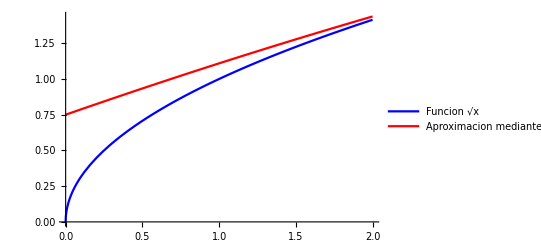

```mathematica
g[x_]:=Log[x]
```

```mathematica
Series[g[x],{x,1,5}]//FullSimplify
```

(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5+O[x-1]^6

```mathematica
Normal[%]
```

-1-1/2 (-1+x)^2+1/3 (-1+x)^3-1/4 (-1+x)^4+1/5 (-1+x)^5+x

```mathematica
Plot[{g[x],-1-1/2 (-1+x)^2+1/3 (-1+x)^3-1/4 (-1+x)^4+1/5 (-1+x)^5+x},{x,0,2},PlotLegends->Automatic,PlotStyle->{Blue,Green}]
```

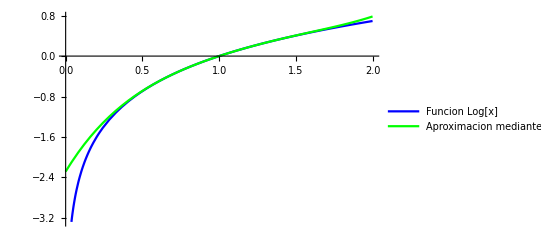

Error en serie de taylor determinar el numero de terminos

```mathematica
R[x_,n_]:=((f)^(n+1)(a))/((n+1)!)x^(n+1);
```

```mathematica
TrueQ[3^2/((10)!)<10^-2]"Numero de terminos para que el error sea inferior a 10^-1"
```

Numero de terminos para que el error sea inferior a 10^-1 True